H(ⅉω)= 1/((1+(ⅈ ω)/80) (1+(ⅈ ω)/60) (1+(ⅈ ω)/40) (1+(ⅈ ω)/20))

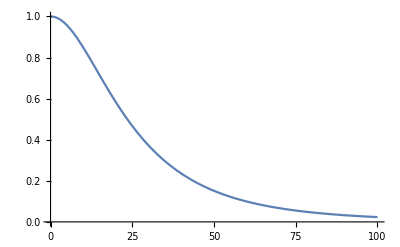

```mathematica
(*Start of Program*)
Clear["Global`*"]
n = Input["Enter The Number Of Poles"];
listOfPoles =Table[Input["Enter The Value Of The Pole"],n];
listOfTerms=(1/(1+(ⅉ ω)/#))&[listOfPoles];
largestPole=Max[listOfPoles];
(*H=Times@@listOfTerms*)
H[ω_]:=Times@@(1/(1+(ⅉ ω)/#))&[listOfPoles](*This makes the function ∏_(i=1)^n 1/(1+ⅉω/Subscript[p, i])*)
StringForm["H(ⅉω)= ``",H[ω]]
peakMag = FindMaximum[Abs[H[ω]],ω][[1]];
Plot[Abs[H[ω]],{ω,0,100},PlotRange->{{0,100},{0,peakMag}}]
```